# Graph Thickness: Effectiveness of Randomized Algorithms

## Sean Adams, Scott Meyer, Sean Meyer

## Outline

Theoretical upper bounds on thickness for each graph

Research into known algorithms and techniques for finding thickness

Our thickness algorithm

Results for competition graphs

Comparison of our results to previous results

## Theoretical Upper Bounds

We came across several formulas1 for thickness that we combined to calculate an upper bound on thickness, in order to have something to judge our results against.

### Formulas

Here are the formulas we found for thickness.

Here’s the results for each graph.

## Research

Here is what we found from our research:

A common, and reasonably effective, heuristic approach to finding thickness is to extract maximal planar subgraphs until the resulting graph is planar2

We might want to have an explanation of what a maximal planar subgraph is here? Not sure.

Somewhat surprisingly, a naive random algorithm is actually very effective at finding good maximal planar subgraphs3

### Effectiveness of Random (Nï) Algorithm for Maximal Planar Subgraphs -Graphics- -Graphics-

These graphs, taken from (3), show two things about this algorithm:

It's effective at finding dense planar subgraphs

Those subgraphs minimize edge crossings when the remaining edges are added back in

Based on these results, we decided to test how well the Nï algorithm would perform for thickness—for both a single run and a prolonged period.

## Our Algorithm

### Thickness

Input: graph G = (V, E)
	Output: thickness of G
	begin
		t = 1
		while G is not planar
			t = t + 1
			G’ = maximal planar subgraph of G
			E’ = edges of G’
			G = G(E\E’)
		return t
	end

### Maximal Planar Subgraph

Input: graph G = (V, E)
	Output: maximal planar subgraph
	begin
		edges = shuffle(E)
		subgraph = (V, ∅)
		for each edge of edges
			temp = subgraph + edge
			if temp is planar
				subgraph = temp
		return subgraph
	end

## Results for Competition Graphs

Below shows the thickness values we got for each graph, both after running the random algorithm once and for 3 hours.

Graph | 1 Run | 3 Hours | Theoretical
K5 | 2 | □ | 2
K8 | 2 | □ | 2
K9 | 3 | □ | 3
Graph1 | 3 | □ | □
Graph2 | 3 | □ | □
Graph3 | 3 | □ | □
Graph4 | 3 | □ | □
MysteryGraph1 | 3 | 2 | □
MysteryGraph2 | 3 | □ | □
MysteryGraph3 | 3 | □ | □

Since the values for most of the graphs are unknown we can’t be sure how accurate these numbers are, but we did definitely get the correct value at least for Mystery Graph 1. The others are all either correct or off by just one, so we are quite pleased with the results. Random variations did result in improvement for one graph, but not on any of the others.

## Comparison to Previous Results

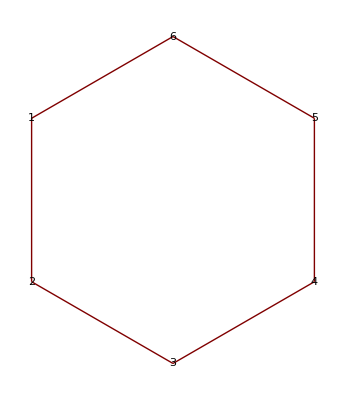

```mathematica
GraphPlot[CycleGraph[6],VertexLabeling->True]
```

## Bipartite, continued

A complete bipartite graph K_(m,n) is a bipartite graph in which S_1contains m vertices, S_2 contains n vertices, and all possible adjacencies between elements of  S_1 and of S_2 occur.

```mathematica
Manipulate[CompleteGraph[{i,j}],{i,1,10,1},{j,1,10,1}]
```

In general, K_(1,n) is called an n-star.

4. A simple path  with n vertices (n>1), written P_n, is given by P_n=(V(P_n), E(P_n)), where

V(P_n)={1,2,3,…,n} and

E(P_n)={(i,i+1): 1≤i≤n-1}.

We write P_n=v_1…v_n, where v_iv_(i+1)∈E(P_n) for i=1,…,n-1.

```mathematica
Manipulate[PathGraph[Range[i]],{i,2,15,1}]
```

## Graph classes, continued

5. A simple cycle with n vertices (n≥3), written C_n, is the graph of P_n with one additional edge, namely (1,n) or v_1v_n. In general, we write C_n=v_0v_1… v_n, where v_0=v_n.

```mathematica
Manipulate[CycleGraph[i],{i,3,30,1}]
```

Modify the code above to include vertex labels.

## Chapter 2, Section 3 [Degree sequence of a finite simple graph]

Let G be a finite simple graph with n vertices whose degrees are given by
 d_1≥d_2≥d_3⋯≥d_n.  Then d_1, d_2, …, d_n is called the degree sequence of G.

### Example 3: Find the degree sequence of each graph below.

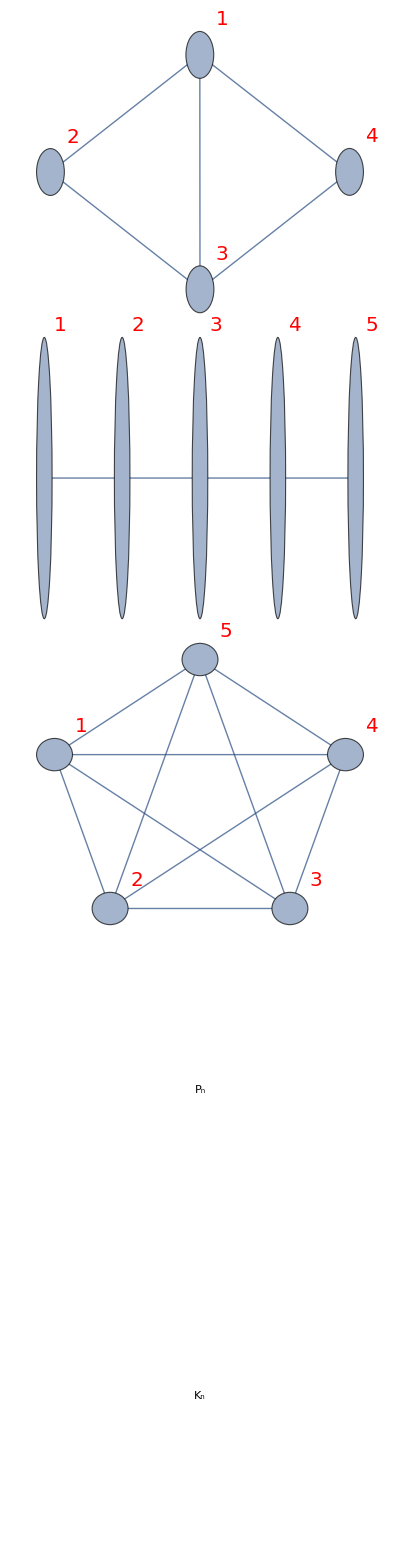

```mathematica
GraphicsGrid[{{f1},{f2},{f3},{eText[Subscript[P, n],0,0,30]},{eText[Subscript[K, n],0,0,30]}},Spacings->-40]
```

## Degree sequences, continued

### Fact.

If G_1≈ G_2 then the degree sequences for G_1and G_2 are the same.

The converse is not necessarily true, though!

### Theorem 2.1

Let G be a finite simple graph with n vertices with degree sequence d_1, d_2, … , d_n. Then ∑_(i=1)^n d_i = 2|E(G)|.

In words, the sum of the degrees of the vertices of a graph is twice the number of edges of the graph.

Proof. Each edge is incident with exactly two vertices, which means that the sum of the degrees double counts the elements of E(G). ▮

## Examples

Construct a graph with degree sequence 5, 4, 3, 3, 2, 1, 0

Construct a graph with degree sequence  4, 4, 3, 3, 2, 2

Construct a graph with degree sequence  1,1,1,1,1,1,1,1,1,1,1

Construct a graph with degree sequence 1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1

Construct a graph with degree sequence 5,5,5,5,5,5,5,5

Construct a graph with degree sequence 2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1

Construct a graph with degree sequence 3,3,3,3,3,3

Construct a graph with degree sequence 3,3,3,3,3,3,3,3

Construct a graph with degree sequence 5,5,5,5,5,5,5,5,5,5,5,5

Construct a graph with degree sequence 3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3

Construct a graph with degree sequence 200, 1,1,…,1 (200 1s)

## More vocabulary and results

### Definition 2.3 [k-regular graph]

If G is a graph for which deg(v)=k ∀v∈V(G), then G is said to be a k-regular graph.

Examples.

C_n is a 2-regular graph.

K_n is an n-1-regular graph.

For which pairs (m,n) is K_(m,n) regular? Only when m=n.

## Chapter 2, Section 4 [About subgraphs]

Question. When is one graph contained in another?

### Definition 2.4 [Subgraph]

Let H=(V(H), E(H)) and G=(V(G), E(G)). 

(a) If V(H)⊂ V(G) and E(H)⊂E(G) then we say that H is a subgraph of G.  We sometimes write H⊂G or H<G.

(b) Alternatively, we say that G is a supergraph of H.

(c) Any graph that is isomorphic to a subgraph of G is considered to be a subgraph of G.

(d) If H⊂G but H≠G, then H is called a proper subgraph  of G. 

(e) If V(G)=V(H) then H is called a spanning subgraph of G.

## Subgraphs, continued

Observation. Any simple graph on n vertices is a spanning subgraph of K_n.

### Definition 2.5[Induced subgraph]

Let G be a graph and V=V(G). If U is a subset of V (ie, U⊂V) then G[U], the subgraph induced by vertex set U, is the graph consisting of the set of all edges with both endpoints in U together with the vertex set U.

## Problem

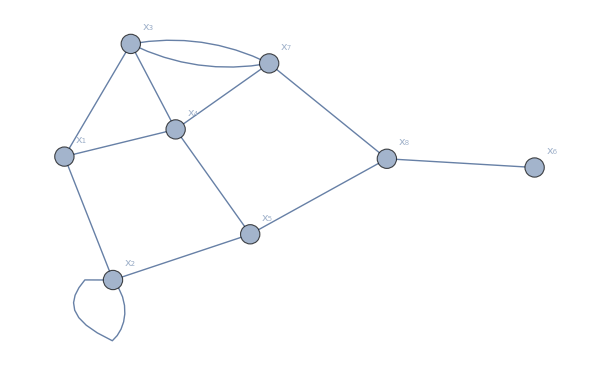

a) What is the simple graph underlying graph G above?

b) Find G-U where U = {x_1,x_3,x_5,x_7}.

c) Find G[U] where U = {x_2,x_3,x_4,x_7}.

d) Find a subgraph of G that is isomorphic to K_3.

e) Find a set of vertices of G whose induced subgraph is K_3.

f) Does G contain a subgraph isomorphic to K_4?

## Problems, problems, problems

Let G be an undirected graph on n vertices and suppose δ  and Δ are the minimum and maximum  vertex degrees of G respectively. What are the smallest and largest possible values for δ  and Δ?

Answer the above question when G has the constraint that it must be a simple graph.

Suppose you know that a certain simple graph G has seven vertices with δ=3 and Δ=5. Prove that |E(G)|≥12.

In the question above, what is the largest possible number of edges in the graph?

Find a 1-regular graph that has 8 vertices.

Describe all possible 1-regular graphs.

Find a 2-regular graph on 10 vertices? Is your graph unique or are there other possibilities?

Describe all possible 2-regular graphs.

Find a 3-regular graph on 10 vertices.

Explain why there is no such thing as a 3-regular graph with 11 vertices.

Why is it impossible to have a (a priori simple) graph with n vertices that has degree sequence (n-1,n-2,…,1,0)?

## Problems, problems, problems

Let G be a simple graph with n vertices, t of which have degree k, and the remaining vertices all have degree k+1. Prove that t=(k+1)n - 2e, where e=|E(G)|.

Let G be a graph with n vertices and n-1 edges. Prove that G either has an isolated vertex or else a vertex of degree 1.

Let G be a simple regular graph with n vertices and 24 edges. Find all possible values of n and construct such a graph for each value of n on your list.

Draw all non-isomorphic simple graphs three vertices. Do not include duplicate elements.

Draw all non-isomorphic simple graphs four vertices. Do not include duplicate elements.

Draw all non-isomorphic simple graphs five vertices. Do not include duplicate elements.

Construct two simple graphs G_1 and G_2 such that the degree sequences of G_1 and G_2 are the same but G_1and G_2 are not isomorphic. Find five “different” examples of pairs of graphs for this question.

## Mathematica Code for the two Mysterious Graphs

```mathematica
eText[word_, x_, y_, fontSize_] := Graphics[{Black, Text[word, {x, y}, BaseStyle -> {FontWeight -> "Bold", FontSize -> fontSize, FontFamily -> "Arial"}]}];
```

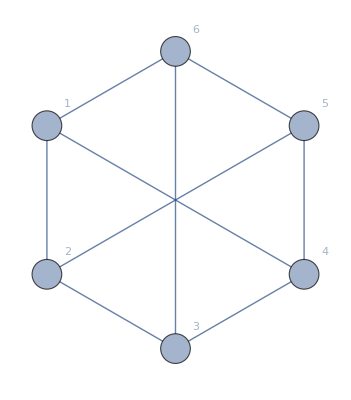

```mathematica
G1=Graph[CirculantGraph[6,{1,3}],VertexLabels->"Name",VertexSize->Medium]
```

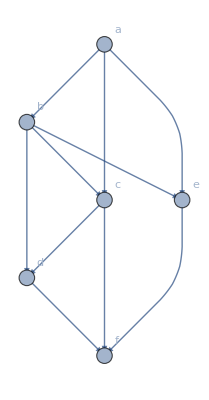

```mathematica
G2=Graph[{a->b,a->c,a->e,b->c,b->d,b->e,c->d,c->f,d->f,e->f},VertexSize->Medium,VertexLabels->"Name"]
```

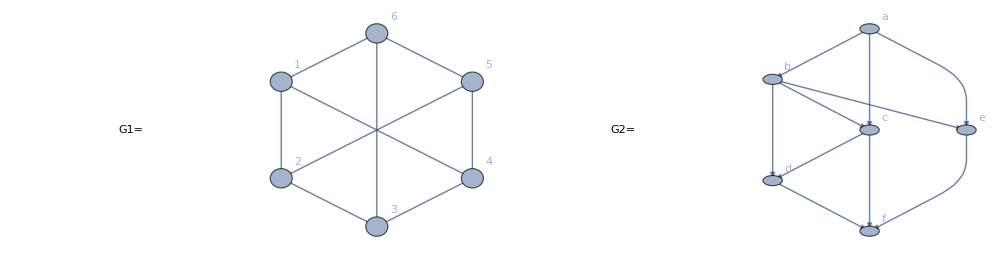

```mathematica
tempPic=GraphicsGrid[{{eText["G1=",0,20,40],G1,eText["G2=",0,20,40],G2}},Spacings->-20,ImageSize->1000]
```

## Mathematica Code for the degree sequence graphs

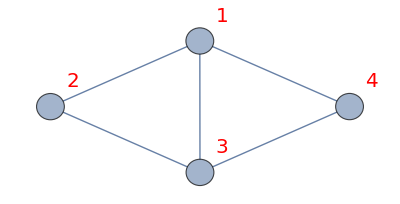

```mathematica
f1=Graph[{1<->2,2<->3,3<->4,1<->4,1<->3},VertexSize->{Medium},VertexLabels->"Name",VertexLabelStyle->Directive[Red,Italic,20]]
```

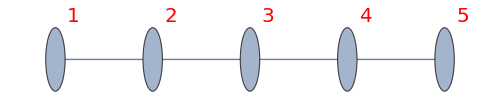

```mathematica
f2=PathGraph[{1,2,3,4,5},VertexSize->{Medium},VertexLabels->"Name",VertexLabelStyle->Directive[Red,Italic,20],ImageSize->500]
```

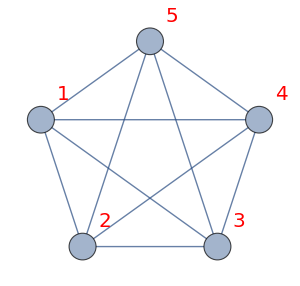

```mathematica
f3=CompleteGraph[5,VertexSize->{Medium},VertexLabels->"Name",VertexLabelStyle->Directive[Red,Italic,20],ImageSize->300]
```

## Mathematica Code for the Induced Subgraph Problem

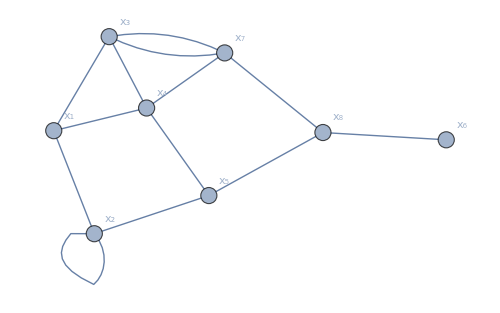

```mathematica
Graph[{1<->2,1<->3,1<->4,2<->2,2<->5,3<->4,3<->7,3<->7,4<->5,4<->7,5<->8,6<->8,7<->8},VertexSize->Medium,VertexLabels->Table[i->Subscript[x,i],{i,8}],ImageSize->500]
```

1	P. Mutzel, T. Odenthal, and M. Scharbrodt. The thickness of graphs: a survey. Graphs and Combinatorics, 14:59–73, 1998.

2	P. Mutzel, T. Odenthal, and M. Scharbrodt. The thickness of graphs: a survey. Graphs and Combinatorics, 14:59–73, 1998.

3	Chimani M., Klein K., Wiedera T. (2016) A Note on the Practicality of Maximal Planar Subgraph Algorithms. In: Hu Y., Nöllenburg M. (eds) Graph Drawing and Network Visualization. GD 2016. Lecture Notes in Computer Science, vol 9801.